```mathematica
Clear[α,β,γ]
```

## Double check rotation matrix and derivatives

```mathematica
rx = {{1,0,0},{0,Cos[α],-Sin[α]},{0,Sin[α],Cos[α]}}
ry = {{Cos[β],0,Sin[β]},{0,1,0},{-Sin[β],0,Cos[β]}}
rz = {{Cos[γ],-Sin[γ],0},{Sin[γ],Cos[γ],0},{0,0,1}}
r = MatrixForm[Dot[rx,ry,rz]]
```

{{1,0,0},{0,Cos[α],-Sin[α]},{0,Sin[α],Cos[α]}}

{{Cos[β],0,Sin[β]},{0,1,0},{-Sin[β],0,Cos[β]}}

{{Cos[γ],-Sin[γ],0},{Sin[γ],Cos[γ],0},{0,0,1}}

(Cos[β] Cos[γ] | -Cos[β] Sin[γ] | Sin[β]
Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ] | Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ] | -Cos[β] Sin[α]
-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ] | Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[α] Cos[β])

(Cos[β] Cos[γ] | -Cos[β] Sin[γ] | Sin[β]
Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ] | Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ] | -Cos[β] Sin[α]
-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ] | Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[α] Cos[β])

```mathematica
drx = MatrixForm[D[Dot[rx,ry,rz],α]]
dry = MatrixForm[D[Dot[rx,ry,rz],β]]
drz = MatrixForm[D[Dot[rx,ry,rz],γ]]
```

(0 | 0 | 0
Cos[α] Cos[γ] Sin[β]-Sin[α] Sin[γ] | -Cos[γ] Sin[α]-Cos[α] Sin[β] Sin[γ] | -Cos[α] Cos[β]
Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ] | Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ] | -Cos[β] Sin[α])

(-Cos[γ] Sin[β] | Sin[β] Sin[γ] | Cos[β]
Cos[β] Cos[γ] Sin[α] | -Cos[β] Sin[α] Sin[γ] | Sin[α] Sin[β]
-Cos[α] Cos[β] Cos[γ] | Cos[α] Cos[β] Sin[γ] | -Cos[α] Sin[β])

(-Cos[β] Sin[γ] | -Cos[β] Cos[γ] | 0
Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ] | -Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ] | 0
Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[α] Cos[γ] Sin[β]-Sin[α] Sin[γ] | 0)

```mathematica
drx
dry
drz
```

(0 | 0 | 0
Cos[α] Cos[γ]-Sin[α] Sin[γ] | -Cos[γ] Sin[α]-Cos[α] Sin[γ] | 0
Cos[γ] Sin[α]+Cos[α] Sin[γ] | Cos[α] Cos[γ]-Sin[α] Sin[γ] | 0)

```mathematica
Simplify[Cos[α] Cos[γ]-Sin[α] Sin[γ]]
```

Cos[α+γ]

```mathematica
rot = {{rxx,rxy,rxz},{ryx,ryy,ryz},{rzx,rzy,rzz}};
MatrixForm[rot]
```

(Cos[β] Cos[γ] | -Cos[β] Sin[γ] | Sin[β]
Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ] | Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ] | -Cos[β] Sin[α]
-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ] | Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[α] Cos[β])

```mathematica
β=Pi/2
```

π/2

```mathematica
rxx = Cos[β] Cos[γ]
rxy=-Cos[β] Sin[γ]
rxz=Sin[β]
ryx=Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ]
ryy=Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ]
ryz=-Cos[β] Sin[α]
rzx=-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]
rzy=Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ]
rzz=Cos[α] Cos[β]
```

0

0

1

Cos[γ] Sin[α]+Cos[α] Sin[γ]

Cos[α] Cos[γ]-Sin[α] Sin[γ]

0

-Cos[α] Cos[γ]+Sin[α] Sin[γ]

Cos[γ] Sin[α]+Cos[α] Sin[γ]

0

```mathematica
Simplify[ryx]
Simplify[ryy]
Simplify[rzx]
Simplify[rzy]
```

Sin[α+γ]

Cos[α+γ]

-Cos[α+γ]

Sin[α+γ]

```mathematica
rotval[α_,β_,γ_]:={{Cos[β] Cos[γ],-Cos[β] Sin[γ],Sin[β]},{Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ],Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ],-Cos[β] Sin[α]},{-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ],Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ],Cos[α] Cos[β]}}
```

```mathematica
α=Pi/3.; 
β=Pi/4.;
γ=Pi/5.;
a=rotval[α,β,γ]
b=rotval[Pi+α,Pi-β,Pi+γ]
rxx
rxy
ryz
rzz
```

{{0.572061,-0.415627,0.707107},{0.789312,0.044565,-0.612372},{0.223006,0.908443,0.353553}}

{{0.572061,-0.415627,0.707107},{0.789312,0.044565,-0.612372},{0.223006,0.908443,0.353553}}

0.572061

-0.415627

-0.612372

0.353553

{{1.11022×10^-16,-1.66533×10^-16,-1.11022×10^-16},{-2.22045×10^-16,-3.33067×10^-16,-3.33067×10^-16},{3.88578×10^-16,0.,-2.22045×10^-16}}

```mathematica
α1 = ArcTan[-rxx/rzz]
-rxx/rzz
Tan[Pi+α1]
Tan[α1]
```

-1.01722

-1.61803

-1.61803

-1.61803

```mathematica
Simplify[(rxx*ryy) -(rxy*ryx)]
Simplify[(rxx*rzy) -(rxy*rzx)]
```

Cos[α] Cos[β]

Cos[β] Sin[α]

Let Mathematica try and solve... Get α,β,γ from rotation matrix

```mathematica
Solve[{Cos[β] Cos[γ]==rxx,-Cos[β] Sin[γ]==rxy,Sin[β]==rxz,Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ]==ryx,Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ]==ryy,-Cos[β] Sin[α]==ryz,-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]==rzx,Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ]==rzy,Cos[α] Cos[β]==rzz},{α,β,γ}]
```

{}

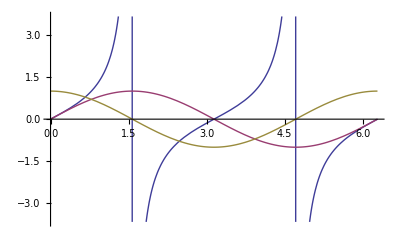

```mathematica
Plot[{Tan[x],Sin[x],Cos[x]},{x,0,2 Pi}]
```

```mathematica
ArcSin[0.5]
```

0.523599

```mathematica
N[0.5235987755982989/°]
```

30.

```mathematica
Sin[Pi-Pi/6]
Sin[Pi/6]
```

1/2

1/2

```mathematica
Cos[-Pi/6]
Cos[-Pi/6]
```

(√3)/2

(√3)/2

```mathematica
Tan[-Pi/6]
Tan[Pi-Pi/6]
```

-1/(√3)

-1/(√3)

{{-(-Sin[β]+Cos[α] Cos[γ] Sin[β]-Cos[β]^2 Sin[α] Sin[γ]-Sin[α] Sin[β]^2 Sin[γ])/(1-Cos[α] Cos[γ]-Cos[β] Cos[γ]+Cos[α] Cos[β] Cos[γ]^2+Sin[α] Sin[β] Sin[γ]+Cos[α] Cos[β] Sin[γ]^2),-(Cos[β] Sin[α]-Cos[β]^2 Cos[γ] Sin[α]-Cos[γ] Sin[α] Sin[β]^2-Cos[α] Sin[β] Sin[γ])/(1-Cos[α] Cos[γ]-Cos[β] Cos[γ]+Cos[α] Cos[β] Cos[γ]^2+Sin[α] Sin[β] Sin[γ]+Cos[α] Cos[β] Sin[γ]^2),1},{-(Cos[α] Cos[β]+1/8 (4-2 Cos[α-β]-2 Cos[α+β]-2 Cos[α-γ]-2 Cos[β-γ]-2 Cos[α+γ]-2 Cos[β+γ]-Sin[α-β-γ]+Sin[α+β-γ]+Sin[α-β+γ]-Sin[α+β+γ]+√(-64+(-4+2 Cos[α-β]+2 Cos[α+β]+2 Cos[α-γ]+2 Cos[β-γ]+2 Cos[α+γ]+2 Cos[β+γ]+Sin[α-β-γ]-Sin[α+β-γ]-Sin[α-β+γ]+Sin[α+β+γ])^2)))/(-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ])+((Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ]) (-Cos[β] Sin[α] (-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ])-(Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ]) (Cos[α] Cos[β]+1/8 (4-2 Cos[α-β]-2 Cos[α+β]-2 Cos[α-γ]-2 Cos[β-γ]-2 Cos[α+γ]-2 Cos[β+γ]-Sin[α-β-γ]+Sin[α+β-γ]+Sin[α-β+γ]-Sin[α+β+γ]+√(-64+(-4+2 Cos[α-β]+2 Cos[α+β]+2 Cos[α-γ]+2 Cos[β-γ]+2 Cos[α+γ]+2 Cos[β+γ]+Sin[α-β-γ]-Sin[α+β-γ]-Sin[α-β+γ]+Sin[α+β+γ])^2)))))/((-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]) (-(Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ]) (Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ])+(-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]) (Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ]+1/8 (4-2 Cos[α-β]-2 Cos[α+β]-2 Cos[α-γ]-2 Cos[β-γ]-2 Cos[α+γ]-2 Cos[β+γ]-Sin[α-β-γ]+Sin[α+β-γ]+Sin[α-β+γ]-Sin[α+β+γ]+√(-64+(-4+2 Cos[α-β]+2 Cos[α+β]+2 Cos[α-γ]+2 Cos[β-γ]+2 Cos[α+γ]+2 Cos[β+γ]+Sin[α-β-γ]-Sin[α+β-γ]-Sin[α-β+γ]+Sin[α+β+γ])^2))))),-(-Cos[β] Sin[α] (-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ])-(Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ]) (Cos[α] Cos[β]+1/8 (4-2 Cos[α-β]-2 Cos[α+β]-2 Cos[α-γ]-2 Cos[β-γ]-2 Cos[α+γ]-2 Cos[β+γ]-Sin[α-β-γ]+Sin[α+β-γ]+Sin[α-β+γ]-Sin[α+β+γ]+√(-64+(-4+2 Cos[α-β]+2 Cos[α+β]+2 Cos[α-γ]+2 Cos[β-γ]+2 Cos[α+γ]+2 Cos[β+γ]+Sin[α-β-γ]-Sin[α+β-γ]-Sin[α-β+γ]+Sin[α+β+γ])^2))))/(-(Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ]) (Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ])+(-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]) (Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ]+1/8 (4-2 Cos[α-β]-2 Cos[α+β]-2 Cos[α-γ]-2 Cos[β-γ]-2 Cos[α+γ]-2 Cos[β+γ]-Sin[α-β-γ]+Sin[α+β-γ]+Sin[α-β+γ]-Sin[α+β+γ]+√(-64+(-4+2 Cos[α-β]+2 Cos[α+β]+2 Cos[α-γ]+2 Cos[β-γ]+2 Cos[α+γ]+2 Cos[β+γ]+Sin[α-β-γ]-Sin[α+β-γ]-Sin[α-β+γ]+Sin[α+β+γ])^2)))),1},{-(Cos[α] Cos[β]+1/8 (4-2 Cos[α-β]-2 Cos[α+β]-2 Cos[α-γ]-2 Cos[β-γ]-2 Cos[α+γ]-2 Cos[β+γ]-Sin[α-β-γ]+Sin[α+β-γ]+Sin[α-β+γ]-Sin[α+β+γ]-√(-64+(-4+2 Cos[α-β]+2 Cos[α+β]+2 Cos[α-γ]+2 Cos[β-γ]+2 Cos[α+γ]+2 Cos[β+γ]+Sin[α-β-γ]-Sin[α+β-γ]-Sin[α-β+γ]+Sin[α+β+γ])^2)))/(-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ])+((Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ]) (-Cos[β] Sin[α] (-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ])-(Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ]) (Cos[α] Cos[β]+1/8 (4-2 Cos[α-β]-2 Cos[α+β]-2 Cos[α-γ]-2 Cos[β-γ]-2 Cos[α+γ]-2 Cos[β+γ]-Sin[α-β-γ]+Sin[α+β-γ]+Sin[α-β+γ]-Sin[α+β+γ]-√(-64+(-4+2 Cos[α-β]+2 Cos[α+β]+2 Cos[α-γ]+2 Cos[β-γ]+2 Cos[α+γ]+2 Cos[β+γ]+Sin[α-β-γ]-Sin[α+β-γ]-Sin[α-β+γ]+Sin[α+β+γ])^2)))))/((-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]) (-(Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ]) (Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ])+(-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]) (Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ]+1/8 (4-2 Cos[α-β]-2 Cos[α+β]-2 Cos[α-γ]-2 Cos[β-γ]-2 Cos[α+γ]-2 Cos[β+γ]-Sin[α-β-γ]+Sin[α+β-γ]+Sin[α-β+γ]-Sin[α+β+γ]-√(-64+(-4+2 Cos[α-β]+2 Cos[α+β]+2 Cos[α-γ]+2 Cos[β-γ]+2 Cos[α+γ]+2 Cos[β+γ]+Sin[α-β-γ]-Sin[α+β-γ]-Sin[α-β+γ]+Sin[α+β+γ])^2))))),-(-Cos[β] Sin[α] (-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ])-(Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ]) (Cos[α] Cos[β]+1/8 (4-2 Cos[α-β]-2 Cos[α+β]-2 Cos[α-γ]-2 Cos[β-γ]-2 Cos[α+γ]-2 Cos[β+γ]-Sin[α-β-γ]+Sin[α+β-γ]+Sin[α-β+γ]-Sin[α+β+γ]-√(-64+(-4+2 Cos[α-β]+2 Cos[α+β]+2 Cos[α-γ]+2 Cos[β-γ]+2 Cos[α+γ]+2 Cos[β+γ]+Sin[α-β-γ]-Sin[α+β-γ]-Sin[α-β+γ]+Sin[α+β+γ])^2))))/(-(Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ]) (Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ])+(-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]) (Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ]+1/8 (4-2 Cos[α-β]-2 Cos[α+β]-2 Cos[α-γ]-2 Cos[β-γ]-2 Cos[α+γ]-2 Cos[β+γ]-Sin[α-β-γ]+Sin[α+β-γ]+Sin[α-β+γ]-Sin[α+β+γ]-√(-64+(-4+2 Cos[α-β]+2 Cos[α+β]+2 Cos[α-γ]+2 Cos[β-γ]+2 Cos[α+γ]+2 Cos[β+γ]+Sin[α-β-γ]-Sin[α+β-γ]-Sin[α-β+γ]+Sin[α+β+γ])^2)))),1}}

## Look at deffernece in angle

```mathematica
α=Pi/3.;
β =Pi/4.;
γ=Pi/5.;
```

```mathematica
Clear[α,β,γ]
```

```mathematica
rx = {{1,0,0},{0,Cos[α+dα],-Sin[α+dα]},{0,Sin[α+dα],Cos[α+dα]}}
ry = {{Cos[β+dβ],0,Sin[β+dβ]},{0,1,0},{-Sin[β+dβ],0,Cos[β+dβ]}}
rz = {{Cos[γ+dγ],-Sin[γ+dγ],0},{Sin[γ+dγ],Cos[γ+dγ],0},{0,0,1}}
TrigExpand[rx]
TrigExpand[ry]
TrigExpand[rz]
r = MatrixForm[Dot[TrigExpand[rx],TrigExpand[ry],TrigExpand[rz]]]
```

{{1,0,0},{0,Cos[dα+α],-Sin[dα+α]},{0,Sin[dα+α],Cos[dα+α]}}

{{Cos[dβ+β],0,Sin[dβ+β]},{0,1,0},{-Sin[dβ+β],0,Cos[dβ+β]}}

{{Cos[dγ+γ],-Sin[dγ+γ],0},{Sin[dγ+γ],Cos[dγ+γ],0},{0,0,1}}

{{1,0,0},{0,Cos[dα] Cos[α]-Sin[dα] Sin[α],-Cos[α] Sin[dα]-Cos[dα] Sin[α]},{0,Cos[α] Sin[dα]+Cos[dα] Sin[α],Cos[dα] Cos[α]-Sin[dα] Sin[α]}}

{{Cos[dβ] Cos[β]-Sin[dβ] Sin[β],0,Cos[β] Sin[dβ]+Cos[dβ] Sin[β]},{0,1,0},{-Cos[β] Sin[dβ]-Cos[dβ] Sin[β],0,Cos[dβ] Cos[β]-Sin[dβ] Sin[β]}}

{{Cos[dγ] Cos[γ]-Sin[dγ] Sin[γ],-Cos[γ] Sin[dγ]-Cos[dγ] Sin[γ],0},{Cos[γ] Sin[dγ]+Cos[dγ] Sin[γ],Cos[dγ] Cos[γ]-Sin[dγ] Sin[γ],0},{0,0,1}}

((Cos[dβ] Cos[β]-Sin[dβ] Sin[β]) (Cos[dγ] Cos[γ]-Sin[dγ] Sin[γ]) | (Cos[dβ] Cos[β]-Sin[dβ] Sin[β]) (-Cos[γ] Sin[dγ]-Cos[dγ] Sin[γ]) | Cos[β] Sin[dβ]+Cos[dβ] Sin[β]
(Cos[dα] Cos[α]-Sin[dα] Sin[α]) (Cos[γ] Sin[dγ]+Cos[dγ] Sin[γ])+(-Cos[α] Sin[dα]-Cos[dα] Sin[α]) (-Cos[β] Sin[dβ]-Cos[dβ] Sin[β]) (Cos[dγ] Cos[γ]-Sin[dγ] Sin[γ]) | (-Cos[α] Sin[dα]-Cos[dα] Sin[α]) (-Cos[β] Sin[dβ]-Cos[dβ] Sin[β]) (-Cos[γ] Sin[dγ]-Cos[dγ] Sin[γ])+(Cos[dα] Cos[α]-Sin[dα] Sin[α]) (Cos[dγ] Cos[γ]-Sin[dγ] Sin[γ]) | (-Cos[α] Sin[dα]-Cos[dα] Sin[α]) (Cos[dβ] Cos[β]-Sin[dβ] Sin[β])
(Cos[α] Sin[dα]+Cos[dα] Sin[α]) (Cos[γ] Sin[dγ]+Cos[dγ] Sin[γ])+(Cos[dα] Cos[α]-Sin[dα] Sin[α]) (-Cos[β] Sin[dβ]-Cos[dβ] Sin[β]) (Cos[dγ] Cos[γ]-Sin[dγ] Sin[γ]) | (Cos[dα] Cos[α]-Sin[dα] Sin[α]) (-Cos[β] Sin[dβ]-Cos[dβ] Sin[β]) (-Cos[γ] Sin[dγ]-Cos[dγ] Sin[γ])+(Cos[α] Sin[dα]+Cos[dα] Sin[α]) (Cos[dγ] Cos[γ]-Sin[dγ] Sin[γ]) | (Cos[dα] Cos[α]-Sin[dα] Sin[α]) (Cos[dβ] Cos[β]-Sin[dβ] Sin[β]))